# Ph20 Homework 5 Philip Carr Friday Section

## Part 1: Simple Problems to Solve

Finding the roots of a 4th-degree polynomial

```mathematica
Roots[t^4+5t^3-10t^2+0.3t-4==0,t]
```

x==-6.54834||x==-0.0666456-0.599 ⅈ||x==-0.0666456+0.599 ⅈ||x==1.68164

Solving a differential equation

```mathematica
DSolve[f''[x]-(k/m)f[x]==0,f[x],x]
```

{{f[x]→ⅇ^((√k x)/(√m)) C[1]+ⅇ^(-(√k x)/(√m)) C[2]}}

## Part 2: Series Expansion Functions for sin(x) and cos(x) to n terms

1.

```mathematica
SerCos[x_,n_]:=Normal[Series[Cos[h],{h,0,n}]]/.h->x
SerSin[x_,n_]:=Normal[Series[Sin[h],{h,0,n}]]/.h->x
```

```mathematica
SerSin[0,10]-Sin[0]
SerSin[0.1,10]-Sin[0.1]
SerSin[0.2,10]-Sin[0.2]
SerSin[0.3,10]-Sin[0.3]
SerSin[0.4,10]-Sin[0.4]
SerSin[0.5,10]-Sin[0.5]
```

0

0.

5.55112×10^-16

4.43534×10^-14

1.04966×10^-12

1.22129×10^-11

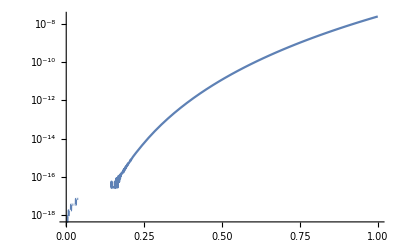

```mathematica
LogPlot[SerSin[x,10]-Sin[x],{x,0,1}]
```

2.

```mathematica
SerCos[h,10]^2+SerSin[h,10]^2
```

(h-h^3/6+h^5/120-h^7/5040+h^9/362880)^2+(1-h^2/2+h^4/24-h^6/720+h^8/40320-h^10/3628800)^2

```mathematica
1.+4.336808689942018*^-19 h^8-2.710505431213761*^-20 h^10+4.592886537331013*^-8 h^12-6.561266481901396*^-9 h^14+2.870554085831863*^-10 h^16-6.075246742501297*^-12 h^18+7.594058428126622*^-14 h^20
```

1.+4.33681×10^-19 h^8-2.71051×10^-20 h^10+4.59289×10^-8 h^12-6.56127×10^-9 h^14+2.87055×10^-10 h^16-6.07525×10^-12 h^18+7.59406×10^-14 h^20

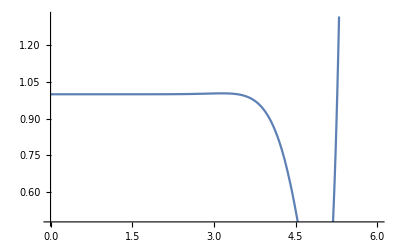

```mathematica
Plot[SerCos[x,10]^2+SerSin[x,10]^2,{x,0,6}]
```

SerCos[x, n]^2 + SerSin[x, n]^2 equals 1 up to x = 4, then the sum diverges from 1, returns to 1 at around x = 5.3, then diverges once more. Algebraically, what goes wrong with the sum is that since the sum is the sum of two series approximations of the functions, which cannot exactly evaluate the sum in the same way that the original sin and cos functions can do. Graphically, as x gets farther away from 0, the series approximations become less accurate, resulting in the sum of squares diverging for relatively large values of x.

```mathematica
SerCosSq[x_,n_]:=Normal[Series[Cos[h]^2,{h,0,n}]]/.h->x
SerSinSq[x_,n_]:=Normal[Series[Sin[h]^2,{h,0,n}]]/.h->x
```

```mathematica
SerCosSq[h,10]+SerSinSq[h,10]
```

1

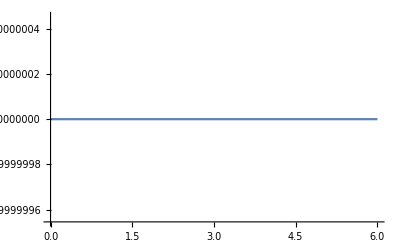

```mathematica
Plot[SerCosSq[x,10]+SerSinSq[x,10],{x,0,6}]
```

The sum of (SerCosSq[x,n] + SerSinSq[x,n]) behaves much more cleanly than the sum of the squares of the series approximations of cos(x) and sin(x), both algebraically and graphically.

## Part 3: Euler Angles

1. Rx[θ], Ry[ζ], and Rz[φ] rotation matrices:

```mathematica
Rx[θ_]:={{1,0,0},{0,Cos[θ],-Sin[θ]},{0,Sin[θ],Cos[θ]}}
Ry[ζ_]:={{Cos[ζ],0,Sin[ζ]},{0,1,0},{-Sin[ζ],0,Cos[ζ]}}
Rz[ϕ_]:={{Cos[ϕ],-Sin[ϕ],0},{Sin[ϕ],Cos[ϕ],0},{0,0,1}}
```

2. General rotation matrix:

```mathematica
Rot3[ψ_,θ_,ϕ_]:=Rz[ψ].Rx[θ].Rz[ϕ]
```

```mathematica
R=Rot3[ψ,θ,ϕ]
```

{{Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ],-Cos[ψ] Sin[ϕ]-Cos[θ] Cos[ϕ] Sin[ψ],Sin[θ] Sin[ψ]},{Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ],Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ],-Cos[ψ] Sin[θ]},{Sin[θ] Sin[ϕ],Cos[ϕ] Sin[θ],Cos[θ]}}

```mathematica
MatrixForm[Simplify[R]]
```

(Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ] | -Cos[ψ] Sin[ϕ]-Cos[θ] Cos[ϕ] Sin[ψ] | Sin[θ] Sin[ψ]
Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ] | Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ] | -Cos[ψ] Sin[θ]
Sin[θ] Sin[ϕ] | Cos[ϕ] Sin[θ] | Cos[θ])

As shown above, the general rotation matrix does not simplify into a relatively clean expression.

3.

```mathematica
Rot3Inverse[ψ_,θ_,ϕ_]:=Rz[-ϕ].Rx[-θ].Rz[-ψ]
```

```mathematica
RI=Rot3Inverse[ψ,θ,ϕ]
MatrixForm[RI.R]
MatrixForm[Simplify[RI.R]]
```

{{Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ],Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ],Sin[θ] Sin[ϕ]},{-Cos[ψ] Sin[ϕ]-Cos[θ] Cos[ϕ] Sin[ψ],Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ],Cos[ϕ] Sin[θ]},{Sin[θ] Sin[ψ],-Cos[ψ] Sin[θ],Cos[θ]}}

(Sin[θ]^2 Sin[ϕ]^2+(Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ])^2+(Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ])^2 | Cos[ϕ] Sin[θ]^2 Sin[ϕ]+(Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ]) (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ])+(-Cos[ψ] Sin[ϕ]-Cos[θ] Cos[ϕ] Sin[ψ]) (Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ]) | Cos[θ] Sin[θ] Sin[ϕ]-Cos[ψ] Sin[θ] (Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ])+Sin[θ] Sin[ψ] (Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ])
Cos[ϕ] Sin[θ]^2 Sin[ϕ]+(Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ]) (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ])+(-Cos[ψ] Sin[ϕ]-Cos[θ] Cos[ϕ] Sin[ψ]) (Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ]) | Cos[ϕ]^2 Sin[θ]^2+(-Cos[ψ] Sin[ϕ]-Cos[θ] Cos[ϕ] Sin[ψ])^2+(Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ])^2 | Cos[θ] Cos[ϕ] Sin[θ]+Sin[θ] Sin[ψ] (-Cos[ψ] Sin[ϕ]-Cos[θ] Cos[ϕ] Sin[ψ])-Cos[ψ] Sin[θ] (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ])
Cos[θ] Sin[θ] Sin[ϕ]-Cos[ψ] Sin[θ] (Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ])+Sin[θ] Sin[ψ] (Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ]) | Cos[θ] Cos[ϕ] Sin[θ]+Sin[θ] Sin[ψ] (-Cos[ψ] Sin[ϕ]-Cos[θ] Cos[ϕ] Sin[ψ])-Cos[ψ] Sin[θ] (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ]) | Cos[θ]^2+Cos[ψ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ψ]^2)

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

4.

```mathematica
MatrixForm[Inverse[Rot3[ψ,θ,φ]].Rot3[ψ,θ,φ]]
```

(((Cos[θ] Cos[ψ] Sin[φ]+Cos[φ] Sin[ψ]) (Cos[θ] Cos[ψ] Sin[φ]+Cos[θ]^2 Cos[φ] Sin[ψ]+Cos[φ] Sin[θ]^2 Sin[ψ]))/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2)+((Cos[φ] Cos[ψ]-Cos[θ] Sin[φ] Sin[ψ]) (Cos[θ]^2 Cos[φ] Cos[ψ]+Cos[φ] Cos[ψ] Sin[θ]^2-Cos[θ] Sin[φ] Sin[ψ]))/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2)+(Sin[θ] Sin[φ] (Cos[ψ]^2 Sin[θ] Sin[φ]+Sin[θ] Sin[φ] Sin[ψ]^2))/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2) | ((Cos[θ] Cos[ψ] Sin[φ]+Cos[θ]^2 Cos[φ] Sin[ψ]+Cos[φ] Sin[θ]^2 Sin[ψ]) (Cos[θ] Cos[φ] Cos[ψ]-Sin[φ] Sin[ψ]))/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2)+((-Cos[ψ] Sin[φ]-Cos[θ] Cos[φ] Sin[ψ]) (Cos[θ]^2 Cos[φ] Cos[ψ]+Cos[φ] Cos[ψ] Sin[θ]^2-Cos[θ] Sin[φ] Sin[ψ]))/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2)+(Cos[φ] Sin[θ] (Cos[ψ]^2 Sin[θ] Sin[φ]+Sin[θ] Sin[φ] Sin[ψ]^2))/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2) | -(Cos[ψ] Sin[θ] (Cos[θ] Cos[ψ] Sin[φ]+Cos[θ]^2 Cos[φ] Sin[ψ]+Cos[φ] Sin[θ]^2 Sin[ψ]))/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2)+(Sin[θ] Sin[ψ] (Cos[θ]^2 Cos[φ] Cos[ψ]+Cos[φ] Cos[ψ] Sin[θ]^2-Cos[θ] Sin[φ] Sin[ψ]))/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2)+(Cos[θ] (Cos[ψ]^2 Sin[θ] Sin[φ]+Sin[θ] Sin[φ] Sin[ψ]^2))/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2)
((-Cos[θ]^2 Cos[ψ] Sin[φ]-Cos[ψ] Sin[θ]^2 Sin[φ]-Cos[θ] Cos[φ] Sin[ψ]) (Cos[φ] Cos[ψ]-Cos[θ] Sin[φ] Sin[ψ]))/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2)+((Cos[θ] Cos[ψ] Sin[φ]+Cos[φ] Sin[ψ]) (Cos[θ] Cos[φ] Cos[ψ]-Cos[θ]^2 Sin[φ] Sin[ψ]-Sin[θ]^2 Sin[φ] Sin[ψ]))/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2)+(Sin[θ] Sin[φ] (Cos[φ] Cos[ψ]^2 Sin[θ]+Cos[φ] Sin[θ] Sin[ψ]^2))/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2) | ((-Cos[ψ] Sin[φ]-Cos[θ] Cos[φ] Sin[ψ]) (-Cos[θ]^2 Cos[ψ] Sin[φ]-Cos[ψ] Sin[θ]^2 Sin[φ]-Cos[θ] Cos[φ] Sin[ψ]))/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2)+((Cos[θ] Cos[φ] Cos[ψ]-Sin[φ] Sin[ψ]) (Cos[θ] Cos[φ] Cos[ψ]-Cos[θ]^2 Sin[φ] Sin[ψ]-Sin[θ]^2 Sin[φ] Sin[ψ]))/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2)+(Cos[φ] Sin[θ] (Cos[φ] Cos[ψ]^2 Sin[θ]+Cos[φ] Sin[θ] Sin[ψ]^2))/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2) | (Sin[θ] Sin[ψ] (-Cos[θ]^2 Cos[ψ] Sin[φ]-Cos[ψ] Sin[θ]^2 Sin[φ]-Cos[θ] Cos[φ] Sin[ψ]))/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2)-(Cos[ψ] Sin[θ] (Cos[θ] Cos[φ] Cos[ψ]-Cos[θ]^2 Sin[φ] Sin[ψ]-Sin[θ]^2 Sin[φ] Sin[ψ]))/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2)+(Cos[θ] (Cos[φ] Cos[ψ]^2 Sin[θ]+Cos[φ] Sin[θ] Sin[ψ]^2))/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2)
((-Cos[φ]^2 Cos[ψ] Sin[θ]-Cos[ψ] Sin[θ] Sin[φ]^2) (Cos[θ] Cos[ψ] Sin[φ]+Cos[φ] Sin[ψ]))/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2)+((Cos[φ] Cos[ψ]-Cos[θ] Sin[φ] Sin[ψ]) (Cos[φ]^2 Sin[θ] Sin[ψ]+Sin[θ] Sin[φ]^2 Sin[ψ]))/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2)+(Sin[θ] Sin[φ] (Cos[θ] Cos[φ]^2 Cos[ψ]^2+Cos[θ] Cos[ψ]^2 Sin[φ]^2+Cos[θ] Cos[φ]^2 Sin[ψ]^2+Cos[θ] Sin[φ]^2 Sin[ψ]^2))/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2) | ((-Cos[φ]^2 Cos[ψ] Sin[θ]-Cos[ψ] Sin[θ] Sin[φ]^2) (Cos[θ] Cos[φ] Cos[ψ]-Sin[φ] Sin[ψ]))/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2)+((-Cos[ψ] Sin[φ]-Cos[θ] Cos[φ] Sin[ψ]) (Cos[φ]^2 Sin[θ] Sin[ψ]+Sin[θ] Sin[φ]^2 Sin[ψ]))/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2)+(Cos[φ] Sin[θ] (Cos[θ] Cos[φ]^2 Cos[ψ]^2+Cos[θ] Cos[ψ]^2 Sin[φ]^2+Cos[θ] Cos[φ]^2 Sin[ψ]^2+Cos[θ] Sin[φ]^2 Sin[ψ]^2))/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2) | -(Cos[ψ] Sin[θ] (-Cos[φ]^2 Cos[ψ] Sin[θ]-Cos[ψ] Sin[θ] Sin[φ]^2))/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2)+(Sin[θ] Sin[ψ] (Cos[φ]^2 Sin[θ] Sin[ψ]+Sin[θ] Sin[φ]^2 Sin[ψ]))/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2)+(Cos[θ] (Cos[θ] Cos[φ]^2 Cos[ψ]^2+Cos[θ] Cos[ψ]^2 Sin[φ]^2+Cos[θ] Cos[φ]^2 Sin[ψ]^2+Cos[θ] Sin[φ]^2 Sin[ψ]^2))/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2))

```mathematica
MatrixForm[Simplify[Inverse[Rot3[ψ,θ,φ]].Rot3[ψ,θ,φ]]]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
MatrixForm[Simplify[Inverse[Rot3[ψ,θ,φ]].Rot3[ψ,θ,φ]-RI.R]]
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)